## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)

(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/mm-mesh/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.2031 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.1.0 for Mac OS X x86

date: May 4, 2020, time: 21:02:15

nb: /Users/dantopa/Mathematica_files/nb/ert/rcs/mm-mesh/Element Mesh Generation.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.2031 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

#### functions

#### substitutions

#### modules

## 1

https : // reference.wolfram.com/language/FEMDocumentation/tutorial/ElementMeshCreation.html

### Passing an ElementMesh to NDSolve

#### Set up a region.

```mathematica
Ω=ImplicitRegion[True,{{x,0,2},{y,0,1}}]
```

ImplicitRegion[0≤x≤2&&0≤y≤1,{x,y}]

#### Set up a PDE operator.

```mathematica
op=-Laplacian[u[x,y],{x,y}]-20
```

-20-u^(0,2)[x,y]-u^(2,0)[x,y]

#### Specify boundary conditions.

```mathematica
Γ=DirichletCondition[u[x,y]==0,x==0||x==2]
```

DirichletCondition[u[x,y]==0,x==0||x==2]

#### Solve the PDE.

```mathematica
ufun=NDSolveValue[{op==0,Γ},u,{x,y}∈Ω]
```

InterpolatingFunction[…]

#### Plot a contour plot of the solution with the element mesh from the interpolation function on top.

```mathematica
Show[ContourPlot[ufun[x,y],{x,y}∈Ω,AspectRatio->Automatic],ufun["ElementMesh"]["Wireframe"]]
```

#### Extract the ElementMesh from an interpolating function.

```mathematica
ufun["ElementMesh"]
```

ElementMesh[{{0.,2.},{0.,1.}},{TriangleElement[<598>]}]

#### Define an explicit mesh with four triangle elements.

```mathematica
mesh=ToElementMesh["Coordinates"->{{0.,0.},{1.,0.},{2.,0.},{2.,1.},{1.,1.},{0.,1.}},"MeshElements"->{TriangleElement[{{1,2,5},{5,6,1},{2,3,4},{4,5,2}}]}]
```

ElementMesh[{{0.,2.},{0.,1.}},{TriangleElement[<4>]}]

```mathematica
mesh["Wireframe"]
```

#### Next, the same PDE is solved, this time with only the explicit mesh defined. Solve the PDE with an ElementMesh.

```mathematica
ufun=NDSolveValue[{op==0,Γ},u[x,y],{x,y}∈mesh];
```

```mathematica
Show[ContourPlot[ufun,{x,y}∈mesh,AspectRatio->Automatic],mesh["Wireframe"]]
```

## 3

### Compare an analytical solution of a PDE with a numerical solution computed with a first-order mesh and a second-order mesh.

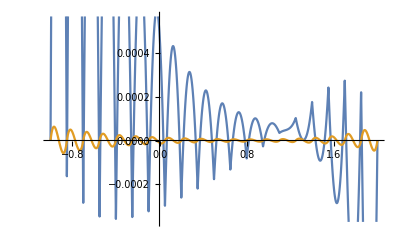

```mathematica
pde=D[-2 u[x],x,x]+3 D[u[x],x]+10 u[x]==1;
exact=DSolveValue[{pde,2*u[-1]==-1,3*u[2]==1/2},u,x];
ufun1=NDSolveValue[{pde,DirichletCondition[2*u[x]==-1,x==-1],DirichletCondition[3*u[x]==1/2,x==2]},u,{x}∈ToElementMesh[FullRegion[1],{{-1,2}},"MeshOrder"->1]];
ufun2=NDSolveValue[{pde,DirichletCondition[2*u[x]==-1,x==-1],DirichletCondition[3*u[x]==1/2,x==2]},u,{x}∈ToElementMesh[FullRegion[1],{{-1,2}},"MeshOrder"->2]];
Plot[{exact[x]-ufun1[x],exact[x]-ufun2[x]},{x,-1,2}]
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```